```mathematica
(*Vs = 36;
Ke=0.0232; (*volts/rad/sec*);
Kt=0.0232; (*Nm/amp*)
r=6;(*ohms*)
*)
```

```mathematica
(*Dcmotor[v_,i_,r_,Ke_,Kt_]:=Module[{ω,τ,p,imax,τmax},
ω=(v-i*r)/Ke;
τ=Kt*i;
p=τ*ω;
imax=v/r;(*Ma*)
τmax=Kt*imax;
Return[{ω,τ,p}];
]*)
```

```mathematica
(*{ω,τ,p}=Dcmotor[Vs,i,r,Ke,Kt];
GraphicsRow[{
Plot[ω,{i,0,Vs/r},AxesLabel->{"current(amps)","Speed(rads/sec)"}],
Plot[τ,{i,0,Vs/r},AxesLabel->{"current(amps)","Torque(Nm)"}],
Plot[p,{i,0,Vs/r},AxesLabel->{"current(amps)","Power(watt)"}]
}]*)
```

max speed of 11m/sec or 40kmph
Acceleration is 0-40kmph in 4 secs .. ie approximately 11/4 = 2.75 m/sec^2 say max 3m/sec^2. The acceleration torque requirement is only for the accelerating the board and for maintaining speed. 

Side ways to wind - Cd = 1.0 - 1.1
Projected area - 0.38 m^2
facing the wind - Cd = 1.2-1.3
Projected area = 0.55
density of air = 1.2kg/m^3

Wheel diameter = 10 inches
Average human mass = 68kg
Mass of the device = 40kg

starting torque = τ Nm

Steady state torque at 40kmph = τ Nm

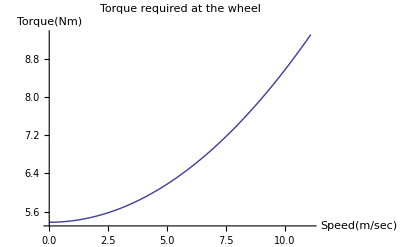

```mathematica
(*
a=3;(*in m/sec^2*)
*)
param={A-> 0.38,ρ-> 1.2,Cd-> 1.1,vmax-> 40*1000/3600,g-> 9.8,C-> 0.04,m-> 68+40,d->10 * 25.4/1000 };
Fd=(ρ*A*Cd*vel^2)/2;
Fr=C*m*g;

F =Fr +Fd;
τreq= F*d/2;(*in Nm*)
wheelrpm=vel/(π*d)*60 ;(*rotations per min*)
Print["starting torque = ",τ/.param/.{vel->0}," Nm"];
Print["Steady state torque at 40kmph = ",τ/.{vel->vmax}/.param," Nm"];
Plot[τreq/.param,{vel,0,vmax/.param},AxesLabel->{"Speed(m/sec)","Torque(Nm)"},PlotLabel-> "Torque required at the wheel"]
(**)
```

```mathematica
p=800;(*in watts*)
(*after transmission efficiecy and motor efficiency*)
p=p*0.75*0.75;
τmotor=rpm*2π/60 (*max torque the motor is capable of delivering*)
```

(π rpm)/30

```mathematica
x=10
```

10